```mathematica
γ=3558/1000
Ω=1118/1000
β=95/100
Λ=100
```

1779/500

559/500

19/20

100

```mathematica
J[w_]:= γ w Exp[-w/Λ]
nb[w_]:= 1/(Exp[β*w]-1) 
gamma[w_]:=J[w]( 1+nb[w])
```

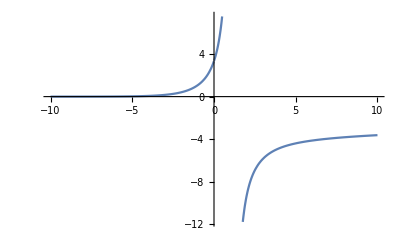

```mathematica
Plot[gamma[w]/(Ω-w),{w,-10,10}]
```

```mathematica
Integrate[gamma[w]/(Ω-w), {w, -Infinity, Infinity}, PrincipalValue->True]
```

GCD::exact: Argument -0.06 in GCD[-0.06,0,0.95,1] is not an exact number.

Integrate[(3.558 ⅇ^(-w/100) (1+1/(-1+ⅇ^(0.95 w))) w)/(1.118-w),{w,-∞,∞},PrincipalValue→True]

```mathematica
Integrate[gamma[w]/(Ω-w), w]
```

3.55881 ∫((1+1/(-1+ⅇ^(0.95 w))) w)/(1.11803-w)ⅆw

```mathematica
γ=3.5588127170858854
Ω=1.118033988749895
β=0.95
Λ=100
```